Computational Journey of Quantum Mechanics | Amir H. Ebrahimnezhad | Advisor: Prf. Ebrahim | University of Tehran

# Quantum Mechanics Principles & Foundations

## Overview

Quantum Mechanics stands as humanity’s most profound and precisely verified theory of nature’s fundamental behavior. Unlike classical physics that governs our everyday experience, quantum mechanics reveals a reality that operates by starkly different rules at the atomic and subatomic scales. This foundational theory rests upon the elegant mathematical framework of linear algebra, offering a relatively accessible mathematical entry point compared to other advanced physical theories like Quantum Field Theory or General Relativity.

Despite its mathematical clarity, quantum mechanics presents conceptual challenges that have confounded even its founding figures. As Richard Feynman famously remarked, “I think I can safely say that nobody understands quantum mechanics.” This paradox—a theory of unparalleled predictive success that defies intuitive understanding—represents one of the most fascinating aspects of modern physics.

This notebook serves as an introduction to the historical development, mathematical foundations, and core principles of quantum mechanics. We will explore the critical experiments that revealed the quantum nature of reality, examine the mathematical formalism that describes quantum systems, and investigate the interpretational challenges that continue to engage physicists and philosophers alike. Through visualizations and conceptual explanations, we aim to build an intuitive foundation for understanding this revolutionary framework, preparing the groundwork for more advanced explorations in subsequent notebooks.

## The Quantum Revolution: History

## The Crisis in Classical Physics (Late 19th Century)

In the second half of the nineteenth century it seemed that the laws of classical mechanics, developed by works of Newton, Lagrange, Hamilton, Jacobi and Poincare, in addition with the Maxwell theory of electromagnetic phenomena completely describe the reality. Despite that we gradually understood that for explaining some particular phenomenas we must reduce to a new kind of mechanics, since classical mechanics would not tackle them at ease. 

Before developing any new ground breaking theory of any sort, a wise scientist would not ruin the palace of older theories, but instead, they would try to a process known as ad-hoc. Adding small adjustments to the current theory in order to make it apply to the current problems. This of course happened before the development of quantum mechanics.

By the early 20th century, there were little to no problem that was challenging by the rich framework of Classical Mechanics (which back then wouldn’t be called classical). But surely some types of problems emerged, making it obvious that we’re facing a new world. The world of modern physics.

## Black Body Radiation and Planck’s Quantum Hypothesis

A blackbody is an idealized physical object that perfectly absorbs and emits electromagnetic radiation. The radiation it emits is called blackbody radiation, and its spectral distribution depends only on the temperature. We here aim to calculate the spectral energy density --the energy per unit volume per unit frequency interval at temperature .

### Classical Derivation

#### Counting Modes

We imagine a cubical  cavity of volume , with perfectly conducting walls. Electromagnetic waves inside the cavity form standing waves. The boundary conditions require the wave vector components to be of below:

```mathematica
V = L^3;
k[nx_,ny_,nz_]:=π/L{nx,ny,nz}
```

The number of modes in wave-vector space within a spherical shell of radius  and thickness  is given by:

```mathematica
dN =2 V/(2π)^3 4π (k^2)dk
```

(dk k^2 L^3)/π^2

The factor 2 accounts for the polarization states of electromagnetic waves. Now the frequency and wave vector are related as following:

```mathematica
dk = 2 π/c dν;
```

```mathematica
dN = dN /. k-> (2π)/c ν
```

(8 dν L^3 π ν^2)/c^3

This gives us the number of modes per unit volume per frequency:

```mathematica
dN/(V dν)
```

(8 π ν^2)/c^3

#### Equipartition of Energy

From classical statistical mechanics (equipartition theorem), each mode has average energy:

```mathematica
averageEnergy = kb T;
```

So the spectral energy density (energy per unit volume per unit frequency):

```mathematica
u[ν_,T_]:=(8π ν^2)/c^3 kb T;
```

#### Ultraviolet Catastrophe

As , . That is, the total energy diverges.

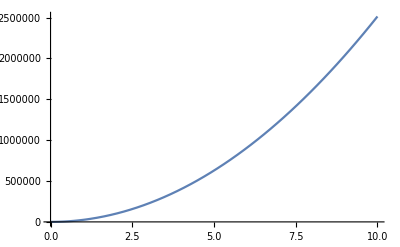

```mathematica
testT = 1000;
c=1;
kb=1;
Plot[u[x,testT], {x,0,10}]
Clear[c, kb];
```

```mathematica
Integrate[u[x,testT],{x,0,Infinity}]
```

Integrate::idiv: Integral of 8000 π x^2 does not converge on {0,∞}.

∫_0^∞ 8000 π x^2ⅆx

Which violets energy conservation and contradicts experimental results... Classical physics breaks down.

### Quantum Derivation

In his attempts to derive the law for the spectral distribution of energy density of a body which is able to absorb all the radiant energy falling upon it, Planck was led to assume that the walls of such a body consist of harmonic oscillators, which exchange energy with the electromagnetic field inside the body only via integer multiples of a fundamental quantity . 

At this stage, to be consistent with another law that had been derived in a thermodynamical way and has and was hence of universal validity, the quantity  turned out to be proportional to the frequency of the radiation field, , and a new constant of nature, , with dimension [energy] [time] and since then called the Planck constant, was introduced for the first time. These problems are part of the general theory of heat radiation (Planck 1991).

#### Same Mode Counting

We use the same density of modes

```mathematica
dN/(V dν)
```

(8 π ν^2)/c^3

#### Quantum Energy Distribution

Now, instead of equipartition, each mode is a quantum harmonic oscillator with discrete energy levels:

```mathematica
e[n_, ν_]:=h n ν
```

The average energy per mode is given by the Boltzmann weighted average:

```mathematica
Clear[averageEnergy];
averageEnergy[ν_,T_]:=(h ν)/(ⅇ^(h ν/kb T)-1)
```

```mathematica
averageEnergy[ν,T]
```

ν/(-1+ⅇ^(0.806452 T ν))

Note: This is the Bose-Einstein occupation number times the quantum energy. So, the energy density becomes:

```mathematica
quantumU[ν_, T_]:=(8 π ν^2)/c^3 averageEnergy[ν, T]
```

#### Planck’s Law

The final result  is known as the Planck distribution, and it matches experimental results perfectly.

```mathematica
quantumU[ν,T]
```

(8 h π ν^3)/(c^3 (-1+ⅇ^((h T ν)/kb)))

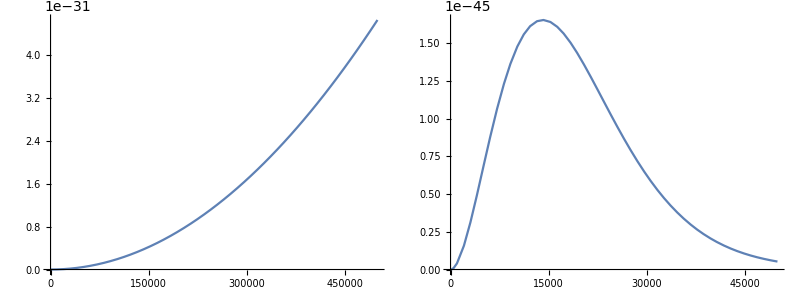

```mathematica
kb=10^-23;
c=3 10^8;
h=10^-32;
testT=200000;
Grid[{{Plot[u[x,testT],{x,0.1,500000} ],
Plot[quantumU[x,testT],{x,0.1,50000}]}}]
Clear[kb,c,testT,h]
```

## Einstein’s Explanation of the Photoelectric Effect

## The Bohr Model of the Atom

## Timeline of Key Discoveries and Contributors

## Wave-Particle Duality:The Cornerstone of Quantum Theory

## De Broglie’s Matter Waves Hypothesis

## Experimental Confirmation:Electron Diffraction

## The Double-Slit Experiment and Its Implications

## Heisenberg’s Uncertainty Principle

## Visualizing Wave-Particle Duality

## Core Principles of Quantum Mechanics

## The Superposition Principle

## Quantum Measurement and Collapse

## Quantum Entanglement and Non-locality

## The Correspondence Principle

## Mathematical Foundations of Quantum Mechanics

## Introduction to Hilbert Spaces

## State Vectors and Wave Functions

## Linear Operators and Observables

## Eigenvalues,Eigenstates,and Measurement

## The Schrödinger Equation as the Quantum Equation of Motion

## Mathematical Formulation of Core Principles

## The Quantum Measurement Problem

## The Copenhagen Interpretation

## The Role of the Observer

## Schrödinger' s Cat Paradox

## Measurement and Decoherence

## Philosophical Implications of Quantum Measurement